```mathematica
Clear["Global`*"]
```

### Constants and Parameters

```mathematica
kB=1.38 10^-23;(*Boltzmann-constant*)
T=273+21; (*temperature of the cell*)
c=3 10^8; (*Speed of light*)
d12=3.5 10^-29; (*dipole-moment for D2 line Rb*)
hbar= 1.054 10^-34; 
ep0=8.854 10^-12;
mass=1.443 10^-25;
muB=9.274*10^-28;(*J G^-1 Bohr's magneton*)
Γ= 2π  6 10^6;(*Spontaneous decay rate*)
K = N@((2 π)/(780 10^-9))(*Wave number*)
```

8.05537×10^6

### Scaling to dimension less variables

```mathematica
x= K/Γ;
maxx= x 300;
scaledvrms =√((kB T K^2)/(mass Γ^2)) 
MB[v_]:= 1/(√(2 π)scaledvrms) Exp[-v^2/(2 scaledvrms^2)]
```

35.829

### Hamiltonian and decay matrices

```mathematica
Subscript[ρ,{i1_,i2_}]:= ρ[i1,i2]
rhomatrix=Table[Subscript[ρ,{i,j}],{i,1,4},{j,1,4}];
rhomatrix1=Flatten[rhomatrix];
H={{0,  0,  -(c13 Ωp)/2, - (c14 Ωp)/2},{0,δp-δc,-(c23 Ωc)/2,-(c24 Ωc)/2},{ -(c31 Ωp)/2, -(c32 Ωc)/2,(δp-Δ-y), 0},{-(c41 Ωp)/2,-(c42 Ωc)/2, 0,(δp-y)}};
commutatormatrix= Dot[H,rhomatrix]-Dot[rhomatrix,H];

anticommutator={{γ (ρ[3,3]+ρ[4,4])+γp (ρ[2,2]-ρ[1,1]),-(γp/2+γd/2) ρ[1,2],-(γ+γp/2+γd/2) ρ[1,3],-(γ+γp/2+γd/2) ρ[1,4] },{-(γp/2+γd/2) ρ[2,1],γ (ρ[3,3]+ρ[4,4])+γp (ρ[1,1]-ρ[2,2]),-(γ+γp/2+γd/2) ρ[2,3],-(γ+γp/2+γd/2) ρ[2,4]},{-(γ+γp/2+γd/2) ρ[3,1],-(γ+γp/2+γd/2) ρ[3,2],-2 γ ρ[3,3],-2 γ ρ[3,4]},{-(γ+γp/2+γd/2) ρ[4,1],-(γ+γp/2+γd/2) ρ[4,2],-2 γ ρ[4,3],-2 γ ρ[4,4]}};
Solutionlist= Flatten[Table[FullSimplify[Solve[0==-I (commutatormatrix[[i,j]])+ anticommutator[[i,j]],rhomatrix[[i,j]]]],{i,1,4},{j,1,4}]];
```

```mathematica
Length[Solutionlist]
```

16

```mathematica
equation=Table[First[Solutionlist[[i]]]==Last[Solutionlist[[i]]],{i,1,16}];
equations1=Join[equation,{ρ[1,1]+ρ[2,2]+ρ[3,3]+ρ[4,4]==1}];
```

```mathematica
Clear[Ωp,Ωc,δp,δc,γp ,γd,γ];
c13=c31=1;
c14=c41=1;
c23=c32=1;
c24=c42=1;
γ=1;
γp=γd=0.0001;
Ωc=2γ;
Ωp=0.1 γ;
δp=0;
Δ=10;
y=m;
new=ParallelTable[table1=Table[{δc,Im[-Last[Solve[equations1,rhomatrix1][[1,4]]]]+Im[-Last[Solve[equations1,rhomatrix1][[1,3]]]]},{δc,-20,20,0.01}];
table1,{m,Range[-20,20,0.01]}];

(*SetSharedVariable[new];
new={};
ParallelDo[
equations=Table[First[Solutionlist[[i]]]==Last[Solutionlist[[i]]],{i,1,9}];
equations1=Join[equations,{ρ[1,1]+ρ[2,2]+ρ[3,3]==1}];
table1=Table[{δp,Im[-Last[Solve[equations1,rhomatrix1][[1,3]]]]},{δp,-5,5,0.01}];
AppendTo[new, table1] ,
{m,Range[-50, 50,0.1]}
]*)
```

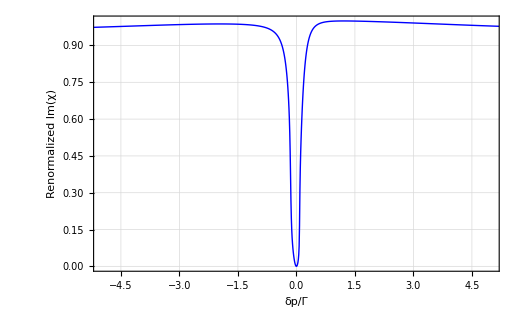

```mathematica
t10 =Table[MB[i],{i,-20,20,0.01}];
t2= Table[i,{i,-20,20,0.01}];
t30=t10.(new[[All,All,2]]);
(*t31=t11.(new1[[All,All,2]]);*)
t4= Table[{t2[[i]],t30[[i]]},{i,1,Length[t2]}];
maxY=Max[t4[[All,2]]];
normalizedTable1={#[[1]],#[[2]]/maxY}&/@t4;
plot1=ListLinePlot[normalizedTable1,PlotStyle->{Directive[Blue,Thick]},
Frame->True,
Axes->False,
ImageSize->520,
PlotRange->{{-5,5},All},
TicksStyle->Directive[Bold,14],
FrameStyle->Directive[Black],
LabelStyle->Directive[Black,Bold,12],(*bold,large labels*)
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->Automatic,
ImagePadding->{{Automatic,Automatic},{Automatic,Scaled[0.01]}},
FrameLabel->{Style["δp/Γ",Bold,16],Style["Renormalized Im(χ)",Bold,16]}]
```

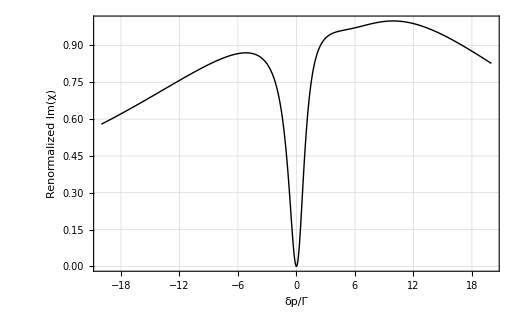

```mathematica
table4=new[[2001]];
maxy4=Max[table4[[All,2]]];
normalizedTable4={#[[1]],#[[2]]/maxy4}&/@table4;
plot4=ListLinePlot[normalizedTable4,PlotStyle->{Directive[Black,Thick]},
Frame->True,
Axes->False,
ImageSize->520,
PlotRange->{{-20,20},All},
TicksStyle->Directive[Bold,14],
FrameStyle->Directive[Black],
LabelStyle->Directive[Black,Bold,12],(*bold,large labels*)
FrameTicks->{{Automatic,None},{Automatic,None}},
GridLines->Automatic,
ImagePadding->{{Automatic,Automatic},{Automatic,Scaled[0.01]}},
FrameLabel->{Style["δp/Γ",Bold,16],Style["Renormalized Im(χ)",Bold,16]}]
```

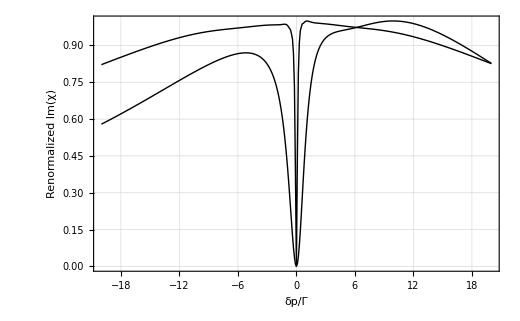

```mathematica
p1= Show[plot1,plot4,PlotRange->{{-20,20},All}]
```